# Transient A-like Current

## Parameters, Equations, Differential Equations

## Parameters

```mathematica
(*parameters*)aParameters={ga->2.2,ek->-80,ka->140,ka1->50,ca2->3.6,va->-12,vb->-62,va2->-40,vx->7,sa->-26,sb->6,sa2->(*-12*)-12,sx->-15,cm->1700(*unit conversion*)};
```

## Steady State Equations

```mathematica
(*equations*)

(*steady states: activation*)
aainfinite[V_]:=1/(1+Exp[(V-va)/sa])/.aParameters;

(*steady states: inactivation 1*)
kbinfinite[V_]:=1/(1+Exp[(V-vb)/sb])/.aParameters;

(*steady states: inactivation 2. I'm using a2 because that's what the text uses consistently. I know, it's confusing.*)
ka2infinite[V_]:=1/(1+Exp[(V-va2)/sa2])/.aParameters;
ka2relaxation[V_]:=ca2/(1+Exp[(V-va2)/sa2])/.aParameters;

(*the weighting factor*)
x[V_]:=1/(1+Exp[(V-vx)/sx])/.aParameters;
```

## Initial Activations/Inactivations

```mathematica
(*find initial activation*)
initialActivation=NDSolve[{aa'[t]==(aainfinite[-40]-aa[t])*ka,aa[0]==0}/.aParameters,aa[t],{t,0,100000}];
```

```mathematica
aa[t]/.initialActivation[[1,All]]/.t->100000
```

0.254089

```mathematica
(*find initial inactivation: part one!*)
initialInactivation1=NDSolve[{ba1'[t]==(kbinfinite[-40]-ba1[t])*ka1,ba1[0]==0}/.aParameters,ba1[t],{t,0,100000}];
```

```mathematica
ba1[t]/.initialInactivation1[[1,All]]/.t->100000
```

0.0249244

```mathematica
(*Find initial inactivation: part two!*)
initialInactivation2=NDSolve[{ba2'[t]==(ka2infinite[-40]-ba2[t])*ka2relaxation[-40],ba2[0]==0}/.aParameters,ba2[t],{t,0,100000}];
```

```mathematica
ba2[t]/.initialInactivation2[[1,All]]/.t->100000
```

0.5

## Differential Equations

```mathematica
(*differential equations*)
{memneg40,memneg30,memneg20,memneg10,mem0,mem10}=Table[NDSolve[{1.7(*cm*)*V'[t]==(-(ga*(aa[t]^3)*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))),aa'[t]==(aainfinite[V[t]]-aa[t])*ka,ba1'[t]==(kbinfinite[V[t]]-ba1[t])*ka1,ba2'[t]==(ka2infinite[V[t]]-ba2[t])*(ka2relaxation[V[t]]),V[0]==initV,aa[0]==0.25408873728969605,ba1[0]==0.02492442664711404,ba2[0]==0.5}/.aParameters,{V[t],aa[t],ba1[t],ba2[t]},{t,0,0.3}],{initV,{-40,-30,-20,-10,0,10}}];
```

## Current Plot

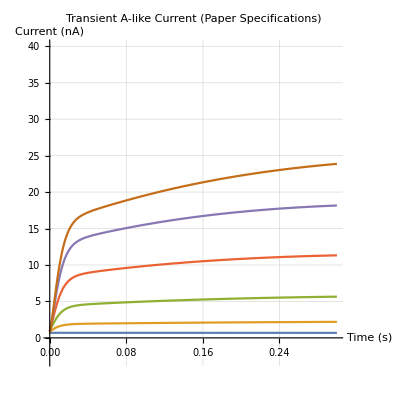

```mathematica
Plot[{Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.memneg40[[1,All]]/.aParameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.memneg30[[1,All]]/.aParameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.memneg20[[1,All]]/.aParameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.memneg10[[1,All]]/.aParameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.mem0[[1,All]]/.aParameters],Evaluate[2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek)/.mem10[[1,All]]/.aParameters]},{t,0,0.3},PlotRange->{{0,0.3},{-3,40}},GridLines->Automatic,AxesLabel->{"Time (s)","Current (nA)"},PlotLabel->"Transient A-like Current (Paper Specifications)",AspectRatio->1]
```

```mathematica
(*this manipulate was built attempting to coax good behavior from the current. Results were not fruitful, and are not included in the final paper due to the lack of quality observations made.*)AManipulate=Manipulate[Plot[Evaluate[(2.2*aa[t]^3*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))/.NDSolve[{1.7(*cm*)*V'[t]==(-(ga*(aa[t]^3)*(x[V[t]]*ba1[t]+(1-x[V[t]])*ba2[t])*(V[t]-ek))),aa'[t]==(aainfinite[V[t]]-aa[t])*ka,ba1'[t]==(kbinfinite[V[t]]-ba1[t])*ka1,ba2'[t]==(ka2infinite[V[t]]-ba2[t])*(ka2relaxation[V[t]]),V[0]==initV,aa[0]==0.25408873728969605,ba1[0]==0.02492442664711404,ba2[0]==0.5}/.{ga->2.2,ek->-80,ka->140,ka1->50,ca2->3.6,va->-12,vb->-62,va2->-40,vx->7,sa->(*-26*)saValue,sb->(*6*)sbValue,sa2->(*-12*)sa2Value,sx->(*-15*)sxValue,cm->1700},{V[t],aa[t],ba1[t],ba2[t]},{t,0,0.3}]],{t,0,0.3},PlotRange->{{0,0.3},{-3,40}},GridLines->Automatic,AxesLabel->{"Time (s)","Voltage (mV)"}],{{sa2Value,-12},-120,-.12},{{sxValue,-15},-150,-1.5},{{saValue,-26},-260,-2.6},{{sbValue,6},0.6,60},{{initv,-40},-40,10}]
```

NDSolve::ndinnt: Initial condition initV is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{1.7 V'[t]==-2.2 aa[t]^3 (Power[«2»] ba1[«1»]+Plus[«2»] ba2[«1»]) (80+V[t]),«6»,ba2[0]==0.5},«1»,{t,0,0.3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 6.12857×10^-6 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{V[6.12857×10^-6],aa[6.12857×10^-6],«1»,ba2[6.12857×10^-6]},{6.12857×10^-6,0,0.3}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 6.12857×10^-6 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{1.7 V'[6.12857×10^-6]==-2.2 aa[«22»]^3 (Power[«2»] ba1[«1»]+«1») (80.+V[6.12857×10^-6]),«7»},«1»,{«1»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.00612858 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

This is the problem graph. It should be Figure3A in the text. However, what we have obtained doesn’t have the spiking behavior observed in the paper, and has similar output from each of the different pulse values, while the paper shows distinctly different behavior for positive and negative voltages. 

To attempt to fix this, Tim and I have reviewed our parameters multiple times, gone over and fixed clerical issues in our steady state equations, and reviewed our initial activation/inactivation calculations. Since our steady state plots below are correct, we are curious if there is an issue with our differential equations above. 

Under the advice of Dr. Chiel, I have changed the exponent on the activation term in the NDSolve, the plot, and the normalized conductance below. Unfortunately none have led to correct behavior.

## Steady State Plots

```mathematica
(*the Aa infinite activation*)aaPlot=Plot[aainfinite[V]/aainfinite[40]/.aParameters,{V,-120,40},GridLines->Automatic,AxesLabel->{"Voltage (mV)","Normalized Values"},PlotLabel->"Transient A-like Steady States and Normalized Conductance",AxesOrigin->{-120,0}];
```

```mathematica
ba1Plot=Plot[kbinfinite[V]/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic,PlotStyle->Orange];
```

```mathematica
normalizedConductance=Plot[(aainfinite[V]*(x[V]*kbinfinite[V]+(1-x[V])*ka2infinite[V]))/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic,PlotStyle->Green,AspectRatio->1];(*removed multiplication by 100, which made it actually show correctly on this scale. I'm unsure why that was included in the paper. Likely, that is a part of our problem with the current graphs above.*)
```

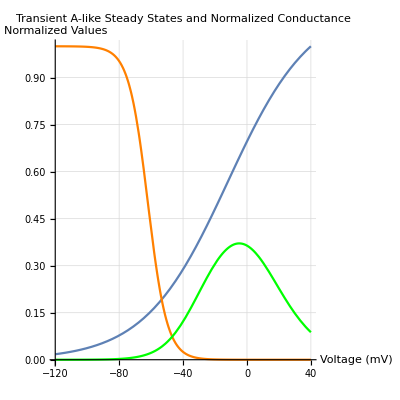

```mathematica
Show[aaPlot,ba1Plot,normalizedConductance,AspectRatio->1]
```

```mathematica
Manipulate[Plot[{(1/(1+Exp[(V-va)/sa]))(*activation*),(1/(1+Exp[(V-vb)/sb]))(*inactivation*),100*(1/(1+Exp[(V-va)/sa]))^3*((x[V]*(1/(1+Exp[(V-vb)/sb])))+((1-x[V])*1/(1+Exp[(V-va2)/12])))(*norm conductance*)}/.{ga->2.2,ek->-80,ka->140,ka1->50,ca2->3.6,va->(*-12*)vaVaried,vb->(*-62*)vbVaried,va2->(*-40*)va2Varied,vx->7,sa->-26,sb->6,sa2->-12,sx->-15,cm->1700},{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic],{{vaVaried,-12},-100,100},{{vbVaried,-62},-100,100},{{va2Varied,-40},-100,100}]
```

```mathematica
aaTimesBa1Plot=Plot[aainfinite[V]*kbinfinite[V],{V,-120,40},PlotStyle->Gray];
```

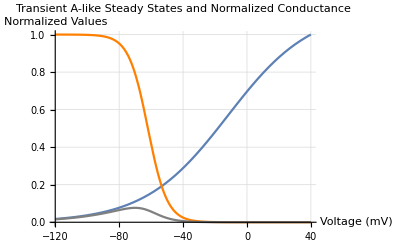

```mathematica
Show[aaPlot,ba1Plot,aaTimesBa1Plot]
```

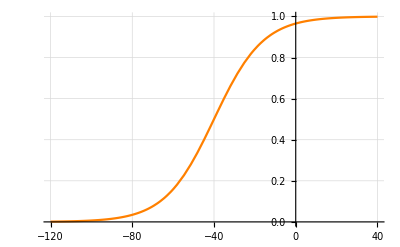

```mathematica
ba2Plot=Plot[ka2infinite[V]/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0.0,1.0}},GridLines->Automatic,PlotStyle->Orange]
```

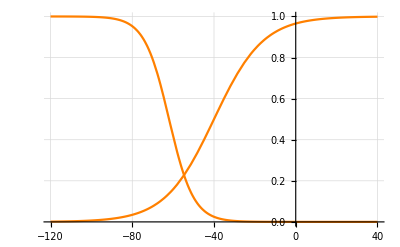

```mathematica
Show[ba2Plot,ba1Plot]
```

```mathematica
ba2RelaxationPlot=Plot[ka2relaxation[V]/ka2relaxation[40]/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic,PlotStyle->Orange];
```

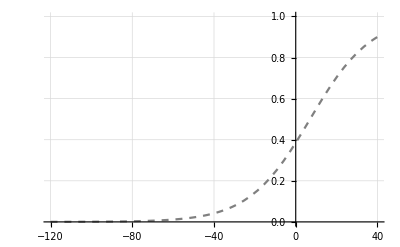

```mathematica
weightingFactorPlot=Plot[x[V]/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic,PlotStyle->{Gray,Dashed}]
```

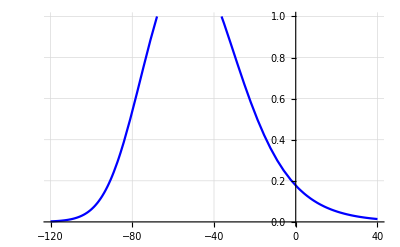

```mathematica
normConductanceTry2=Plot[aainfinite[V+50]*(x[V+50]*kbinfinite[V+50]+(1-x[V+50])*ka2infinite[V+50]*ka2relaxation[V+50])/.aParameters,{V,-120,40},PlotRange->{{-120,40},{0,1}},GridLines->Automatic,PlotStyle->Blue]
```

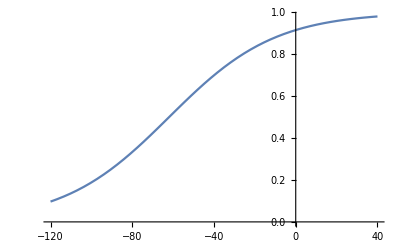

```mathematica
aaTransplantedBy50=Plot[aainfinite[V+50]/.aParameters,{V,-120,40}]
```

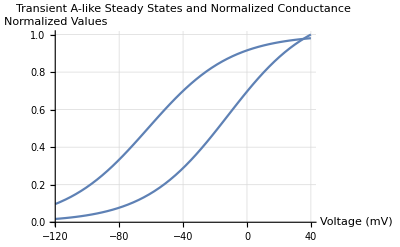

```mathematica
Show[aaPlot,aaTransplantedBy50]
```

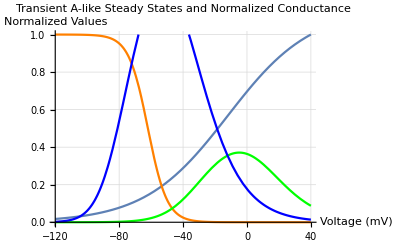

```mathematica
Show[aaPlot,ba1Plot,normalizedConductance,normConductanceTry2]
```

Our activation and first inactivation match the paper’s results perfectly. The normalized current, who’s equation we reviewed with you in class, appears to be offset by some constant amount. Timothy worked with Jon in office hours to build a manipulate that allowed him to move the normalized conductance curve by changing time by a constant amount. That seems to me like a bit of a hack -- I am expectant that the issue lies somewhere in our current equation implementation.